```mathematica
Function[x,((1.03961212 x^2)/(x^2-0.00600069867)+(0.231792344 x^2)/(x^2-0.0200179144)+(1.01046945 x^2)/(x^2-103.560653))/(√((1.03961212 x^2)/(x^2-0.00600069867)+(0.231792344 x^2)/(x^2-0.0200179144)+(1.01046945 x^2)/(x^2-103.560653)+1))]
```

```mathematica
Function[x,((1.03961212 x^2)/(x^2-0.00600069867)+(0.231792344 x^2)/(x^2-0.0200179144)+(1.01046945 x^2)/(x^2-103.560653))/(√((1.03961212 x^2)/(x^2-0.00600069867)+(0.231792344 x^2)/(x^2-0.0200179144)+(1.01046945 x^2)/(x^2-103.560653)+1))*(2.998x/2Pi)]
```

Function[x,(((1.03961 x^2)/(x^2-0.0060007)+(0.231792 x^2)/(x^2-0.0200179)+(1.01047 x^2)/(x^2-103.561)) (2.998 x π))/(√((1.03961 x^2)/(x^2-0.0060007)+(0.231792 x^2)/(x^2-0.0200179)+(1.01047 x^2)/(x^2-103.561)+1) 2)]

```mathematica
%8[0.7]
```

2.8091

```mathematica
%8[0.65]
```

2.61485

```mathematica
%8[0.6]
```

2.42091

```mathematica
%8[0.55]
```

2.22744

```mathematica
%8[0.5]
```

2.0347

```mathematica
%8[0.45]
```

1.84308

```mathematica
%8[0.4]
```

1.65316

SetDelayed::wrsym: Symbol x is Protected.

```mathematica
Function[x,(1.03961212 x^2)/(x^2-0.00600069867)+(0.231792344 x^2)/(x^2-0.0200179144)+(1.01046945 x^2)/(x^2-103.560653)]
```

Function[x,(1.03961 x^2)/(x^2-0.0060007)+(0.231792 x^2)/(x^2-0.0200179)+(1.01047 x^2)/(x^2-103.561)]

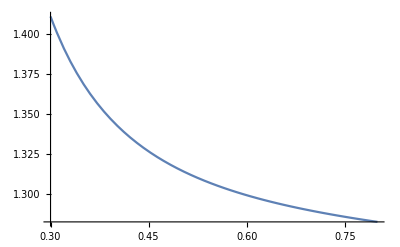

```mathematica
Plot[Function[x,(1.03961212 x^2)/(x^2-0.00600069867)+(0.231792344 x^2)/(x^2-0.0200179144)+(1.01046945 x^2)/(x^2-103.560653)][x],{x,0.3,0.8}]
```

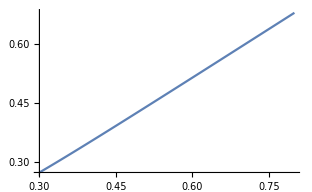

```mathematica
Plot[Function[x,((1.0396 x^3)/(x^2-0.006)+(0.2318 x^3)/(x^2-0.02)+(1.01 x^3)/(x^2-103.561))/Sqrt[(1.0396 x^2)/(x^2-0.006)+(0.2318 x^2)/(x^2-0.02)+(1.01 x^2)/(x^2-103.561)+1]][x],{x,0.3,0.8}]
```

```mathematica
(1.0396 x^2)/(x^2-0.006)+(0.2318 x^2)/(x^2-0.02)+(1.01 x^2)/(x^2-103.561)
```

(1.01 x^2)/(-103.561+x^2)+(0.2318 x^2)/(-0.02+x^2)+(1.0396 x^2)/(-0.006+x^2)

```mathematica
Simplify[(1.01 x^2)/(-103.561+x^2)+(0.2318 x^2)/(-0.02+x^2)+(1.0396 x^2)/(-0.006+x^2)]
```

(2.29739 x^2-131.716 x^4+2.2814 x^6)/(-0.0124273+2.69271 x^2-103.587 x^4+x^6)

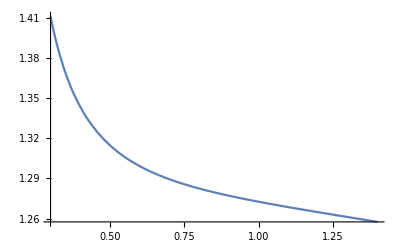

```mathematica
Plot[(2.2973941508 x^2-131.71589820000003 x^4+2.2814 x^6)/(-0.012427320000000002+2.6927060000000003 x^2-103.587 x^4+x^6),{x,0.3,1.4}]
```

```mathematica
Function[x,(2.2973941508 x^2-131.71589820000003 x^4+2.2814 x^6)/((-0.012427320000000002+2.6927060000000003 x^2-103.587 x^4+x^6)Sqrt[4*Pi^2/x^2-Pi^2/9])]
```

```mathematica
Simplify[(2.2973941508 x^2-131.71589820000003 x^4+2.2814 x^6)/((-0.012427320000000002+2.6927060000000003 x^2-103.587 x^4+x^6)Sqrt[4*Pi^2/x^2-Pi^2/9])]
```

(2.19385 x^2-125.779 x^4+2.17858 x^6)/(√(-1+36/x^2) (-0.0124273+2.69271 x^2-103.587 x^4+x^6))

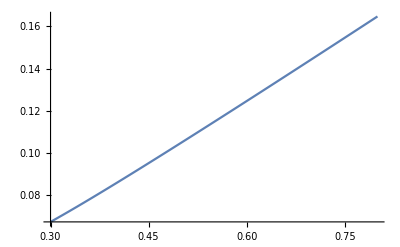

```mathematica
Plot[(2.1938498119813636 x^2-125.77941769391333 x^4+2.1785765230191005 x^6)/(√(-1+36/x^2) (-0.012427320000000002+2.6927060000000003 x^2-103.587 x^4+x^6)),{x,0.3,0.8}]
```

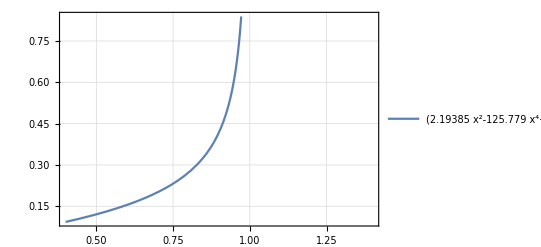

```mathematica
Plot[(2.1938498119813636 x^2-125.77941769391333 x^4+2.1785765230191005 x^6)/(√(-36+36/x^2) (-0.012427320000000002+2.6927060000000003 x^2-103.587 x^4+x^6)),{x,0.4,1.4},PlotTheme->"Detailed"]
```

```mathematica
Simplify[(2.6734 x^2)/(-0.01764+x^2)+(1.2290 x^2)/(-0.05914+x^2)+(12.614 x^2)/(-474.60+x^2)]
```

(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)

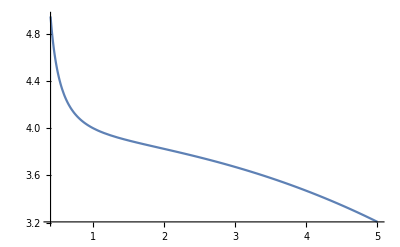

```mathematica
Plot[(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6),{x,0.4,5}]      (*n^2-1 for LiNbO3*)
```

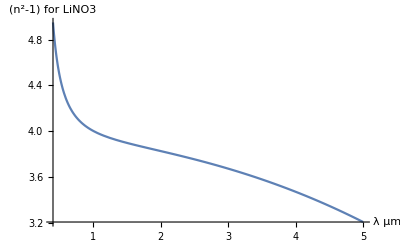

```mathematica
Show[%113,AxesLabel->{HoldForm[λ µm],HoldForm[(n^2-1)for LiNO3]},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold,Italic}]
```

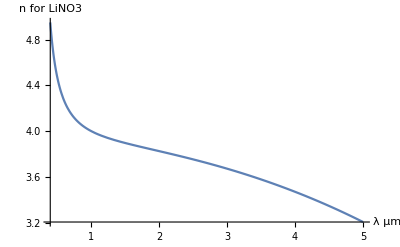

```mathematica
Show[%116,AxesLabel->{HoldForm[λ µm],HoldForm[HoldForm[n for LiNO3]]},PlotLabel->None]
```

```mathematica
Show[%116,AxesLabel->{HoldForm[λ µm],HoldForm[HoldForm[n for LiNO3]]},PlotLabel->None]
```

-Graphics-

```mathematica
Simplify[Sqrt[(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)+1]]
```

√(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6))

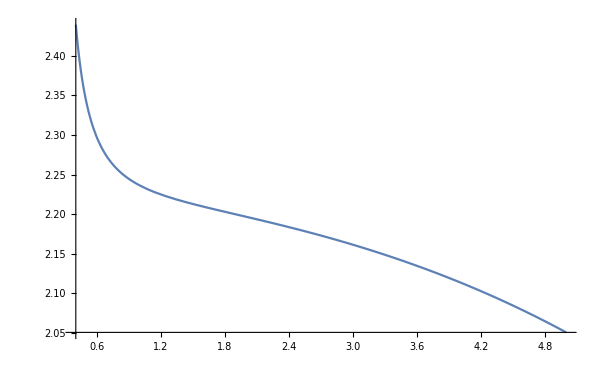

```mathematica
Plot[√(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)),{x,0.4,5}]          (*n for LiNbO3*)
```

```mathematica
Simplify[((85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))(x-0.3)/√(-1+36/x^2) ]
```

((-0.3+x) (85.3389 x^2-1853.23 x^4+16.5164 x^6))/(√(-1+36/x^2) (-0.495117+36.4408 x^2-474.677 x^4+x^6))

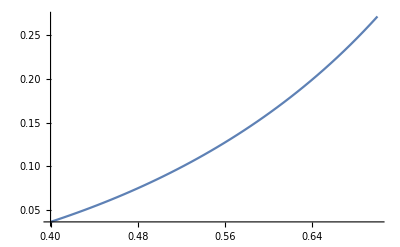

```mathematica
Plot[((-0.3+x) (85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6))/(√(-36+36/x^2) (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)),{x,0.4,0.7}]
```

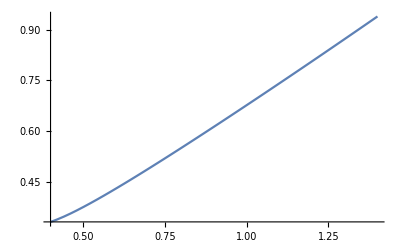

```mathematica
Plot[(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(√(-1+36/x^2) (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)),{x,0.4,1.4}]
```

```mathematica
Plot[(14.2231421039624 x^2-308.87122122600005 x^4+2.7527333333333335 x^6)/(√(-1+1/x^2) (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))*3,{x,0.4,0.7}]
```

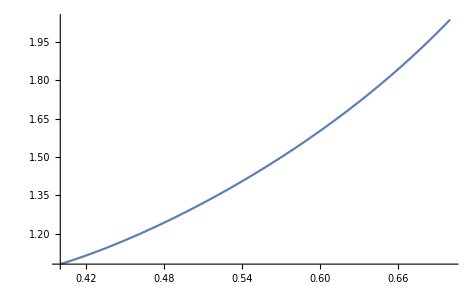

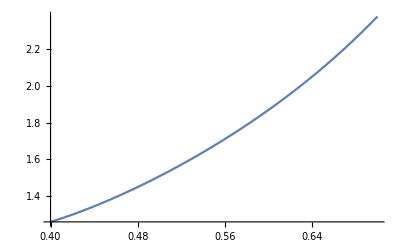

Plot::nonopt: Options expected (instead of PlotTheme m→Scientific) beyond position 2 in Plot[((14.2231 x^2-308.871 x^4+2.75273 x^6) 3.5)/(√(-1+1 Power[«2»]) (-0.495117+36.4408 x^2-474.677 Power[«2»]+x^6)),{x,0.4,0.7},PlotTheme m→Scientific]. An option must be a rule or a list of rules.

```mathematica
Plot[((14.2231421039624 x^2-308.87122122600005 x^4+2.7527333333333335 x^6) 3.5)/(√(-1+1/x^2) (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)),{x,0.4,0.7}]
```

```mathematica
Function[x,(4Pi^2*(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6))/((-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)*x^2*Sqrt[4Pi^2*((85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)+1)/x^2-Pi^2/9])]
```

Function[x,(4 π^2 (85.3389 x^2-1853.23 x^4+16.5164 x^6))/((-0.495117+36.4408 x^2-474.677 x^4+x^6) x^2 √((4 π^2 ((85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)+1))/x^2-π^2/9))]

```mathematica
Simplify[(4 π^2 (85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6))/((-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6) x^2 √((4 π^2 ((85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)+1))/x^2-π^2/9))]
```

(3369.04-73162.5 x^2+652.041 x^4)/((-0.495117+36.4408 x^2-474.677 x^4+x^6) √((-19.5464+4808.21 x^2-91941.9 x^4+1212.06 x^6-1.09662 x^8)/(x^2 (-0.495117+36.4408 x^2-474.677 x^4+x^6))))

```mathematica
Plot[%2,{x,50,500}]
```

-Graphics-

```mathematica
Simplify[(4 π^2 (85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6))/((-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6) x^2 *((4 π^2 ((85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)+1))/x^2-π^2/9))]
```

(-3072.2 x^2+66716.2 x^4-594.59 x^6)/(17.8242-4384.56 x^2+83841. x^4-1105.27 x^6+x^8)

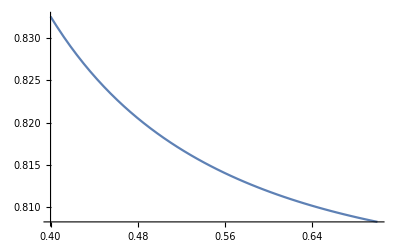

```mathematica
Plot[(-3072.1986944558785 x^2+66716.183784816 x^4-594.5904 x^6)/(17.82420365376-4384.563735489639 x^2+83840.9886960456 x^4-1105.26718 x^6+x^8),{x,0.4,0.7}]
```